# ColorGraphVertices

Color the vertices of a graph so no adjacent nodes have the same color

## Definition

```mathematica
ClearAll[ColorGraphVertices]
ColorGraphVertices[graph_?GraphQ,options:OptionsPattern[Graph]]:=Graph[Annotate[graph,{VertexStyle->Thread[VertexList[graph]->FindVertexColoring[graph,ColorData[106,"ColorList"]]]}],options];

ColorGraphVertices[graph_?GraphQ,colors_List,options:OptionsPattern[Graph]]:=Graph[Annotate[graph,{VertexStyle->Thread[VertexList[graph]->FindVertexColoring[graph,colors]]}],options]
```

## Documentation

### Usage

ColorGraphVertices[graph]

colors the vertices of graph with no adjacent vertices having the same color.

ColorGraphVertices[graph, colors]

uses colors from the color list colors.

### Details & Options

Every planar graph can have colors assigned to its vertices such that no adjacent vertices have the same color with at most four colors according to the four color theorem.

The vertices are colored using ColorData[106] by default.

Finding colorings for graphs is an NP complete problem.

## Examples

### Basic Examples

Color the vertices of the Petersen graph:

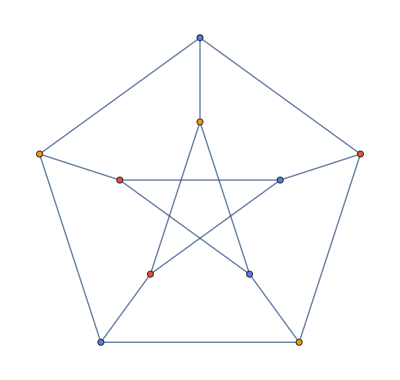

```mathematica
ColorGraphVertices[PetersenGraph[]]
```

Use a different coloring list with ColorData:

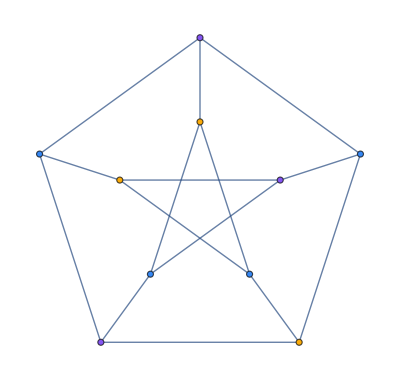

```mathematica
ColorGraphVertices[PetersenGraph[],ColorData[101,"ColorList"]]
```

### Scope

Color the vertices of the skeleton of the Csaszar polyhedron:

```mathematica
MeshConnectivityGraph[PolyhedronData["CsaszarPolyhedron","Polyhedron"],0]//ColorGraphVertices
```

-Graphics3D-

### Applications

Make a large random graph and color the vertices:

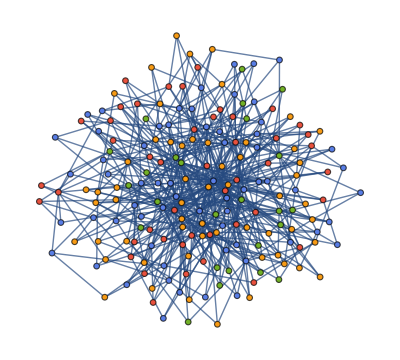

```mathematica
ColorGraphVertices[RandomGraph[BarabasiAlbertGraphDistribution[192,3]],ImageSize->Full]
```

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Graph coloring

Four Color Theorem

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

FindVertexColoring

FindEdgeColoring

FindIndependentEdgeSet

### Related Resource Objects

RandomMixedGraph

AlternatingTreeGraph

RandomWeightedGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.